# Using git at Wolfram

## Table of Contents

Introduction

How to set up git

The basics of using git

Slightly more advanced git

The preferred Wolfram git workflow

## Introduction

Since the early 1990s, Wolfram has used cvs as its standard tool for version control. Wolfram is now moving to a new standard — git.  We expect this to be the standard tool for many years to come, and we are currently engaged in a massive project to convert all of Wolfram’s active code and document repositories over to git.

This document is written to give you a gentle introduction to git, and to the preferred workflows we wish to establish with git.  If you are familiar with git, then you will probably want to skip directly to the last section, which discusses how we wish to use git in the company.  But if you haven’t used git, even if you have used cvs, Mercurial, or Bazaar, you should read the entire document.  Git is very different from cvs, and while it’s much closer to Mercurial and Bazaar, there are still differences which can trip you up.

## How to set up git

### Choice of git client

You may use any git client you wish.  But if you expect support from sysadmin and fellow developers, you should stick with one of the following git clients:

[Mac, Windows] Atlassian SourceTree

[Linux, Mac] The standard command-line git

[Windows] msys-git command-line

[All platforms] Eclipse integrated git support

See the ITFAQ for instructions on how to install and configure git on your system.

### Setting up git on your machine

There are a few configurations which are absolutely required to make sure that git is properly working on your system.  To start with, git must be configured with your name and email address.  And there are some other settings which we prefer at Wolfram.  If you are running git from the command-line, you should execute the following commands:

git config --global user.name "your name"
git config --global user.email email@wolfram.com

# for Windows users only
git config --global core.autocrlf true
git config --global fetch.prune true

In SourceTree, you will be prompted for your name and email address at install time.  If you wish to change this information, it can be found in the SourceTree preferences.

It’s also a good idea to set up a decent merge tool.  On Macintosh, you can use the built-in FileMerge diffing tool.  On Windows or Linux, you’ll need to download a tool.  A good one which supports git is P4Merge.

### Getting access to git.wolfram.com

Git repositories are hosted at stash.wolfram.com.  There is a lot of help and documentation available on the Stash server.  In order to access the server, you must first log in using your regular Wolfram login and password and register your public key.  To register your public key, after you’ve logged in, go to the account management interface:

From here, go to the interface for adding public keys.  Click Add Key, and copy and paste your public key into the form.  Note that your public key is probably in a file which ends with a .pub extension, such as id_rsa.pub.  Never give out your private key, which is in the file without the .pub extension.  This is like giving someone your password.  If you believe your private key has been compromised, it’s important that you generate a new key pair and update your public key ASAP.

You may not have access to all projects or repositories; if you need access, you can access any developer on the relevant project who the project administrators are and request access from them.  However, in order to clone a local copy of the repository or to make changes to the repository, you need to set up a public/private key pair.  You can generate, change, or upload private keys at this website.

Note that your private key is like your password.  You should never give it to anyone, not even to SysAdmin, not even if you have password-protected it.  You should never copy your private key to a public computer.  If you believe your private key has been compromised, it’s important that you generate a new one.  Your public key, on the other hand, may need to be given to a git administrator or others in order to make sure you have proper access.

To test your git access, try using your git client to clone the following git repository:

ssh://git@stash.wolfram.com:7999/misc/test_repo.git

If you try this and you are prompted for a password, then your private/public key pair hasn’t been properly set up.

### The Git Palette

## The basics of using git

### Git usage: a visualization

Git is not like cvs.  A git repository is represented by a directed graph of commits.  Every commit has at least one parent.

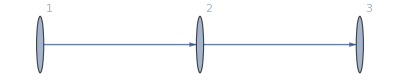

```mathematica
Graph[{1->2, 2->3},VertexLabels->"Name"]
```

If, in this example, you make a commit whose parent is commit 3, and another developer makes a commit whose parent is commit 3 as well, the situation must be resolved:

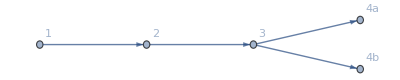

```mathematica
Graph[{1->2, 2->3,3->"4a",3->"4b"},VertexCoordinates->{{0,0},{1,0},{2,0},{3,.2},{3,-.2}},VertexLabels->"Name"]
```

There are two ways to resolve this.  One is to create another commit which is a child of both commits and effectively “merges” them:

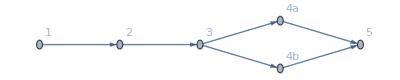

```mathematica
Graph[{1->2, 2->3,3->"4a",3->"4b","4a"->5,"4b"->5},VertexCoordinates->{{0,0},{1,0},{2,0},{3,.2},{3,-.2},{4,0}},VertexLabels->"Name"]
```

The second way to resolve the situation is to take your commit (in this case 3b) and “rebase” it, which is to say that you create an equivalent commit (represented as 4b’) with a new parent:

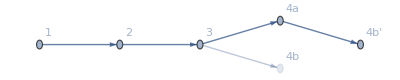

```mathematica
Graph[{1->2, 2->3,3->"4a",3->"4b","4a"->"4b'"},VertexCoordinates->{{0,0},{1,0},{2,0},{3,.2},{3,-.2},{4,0}},VertexLabels->"Name",VertexStyle->{"4b"->Directive[Opacity[0.3],EdgeForm[Opacity[0.3]]]},EdgeStyle->{3->"4b"->Opacity[0.3]}]
```

Discussions below may refer to “merging” or “rebasing” when referring to the above workflows.

### Cloning repositories

The very first time you wish to work with a repository, you need to “clone” it to your system.  To clone a repo, you must have a URI spec which identifies its location on the Stash server. To find this, go to the repository’s page on the Stash server, and click the Clone button:

If you have SourceTree installed, you may be able to just click the button to clone in SourceTree.  Otherwise, you should copy the URI and do the following:

Command-line

# uri = clone uri, dir = local directory to use (optional)
git clone uri dir

SourceTree

File → New, then type in the URI you wish to clone and where you want to store it on your local computer.

### Pulling changes

To get changes which have been pushed by other people, you must “pull” the changes to your system.  By default, you can simply do:

Command-line

git pull --rebase origin master

SourceTree

Click the pull button, ensure the “Rebase” option is checked, and press OK in the resulting dialog.

This may fail if you have local changes you haven’t committed.  If you don’t want to commit your local changes but really want to pull remote changes, then you can stash your changes.

### Committing changes

To commit your changes, you must first add them to the staging area (alternatively known as the index or cache).  The commit command will only commit changes which have been added to the staging area.  Thus the meaning of “add” in git really means to add a change, which is very much unlike cvs where “add” means to add a new file.  In fact, if you wanted to delete a file in git, you would first delete the file, and then “add” the change to the staging area.

Note that committing a change does not make it public, and does not require a network connection.  You can and should commit your changes often to ensure that you don’t lose them, or that you have a record of milestones in your work.

To commit all of the changes in a directory:

Command-line

git add .
git commit

SourceTree

Click the checkmark in the upper-left-hand corner to see a list of changed files.  Staged files are shown at the top, unstaged files at the bottom.  To view the changes in a given file, select the file and the changes will appear on the right.  To stage a file, check the checkbox and it will move from the unstaged area to the staged area.  Click commit when you’re ready to commit.

### Pushing commits

If you have commits which you would like to publish back to the Stash server, you need to “push” them.  A push operation can fail if somebody else beats you to the punch and pushes a change to the existing repo before you do.  If this happens, you’ll receive an appropriate warning, and you’ll need to first pull changes and resolving the issue before you push.

SourceTree will remind you that you have unpushed changes by adding a count of unpushed commits to its Push icon in the toolbar.

Command-line

git push origin master

SourceTree

### Stashing changes

Stashing changes is a convenient way of setting aside some work you’re in the middle of and temporarily reverting to a clean repo.  The changes you made can be reapplied later at your convenience, or can be deleted if they’re no longer necessary.  A stash is like a mini-branch, but one which will never be pushed to a remote machine.  You can have multiple stashes if you wish.

Stashes are not a good tool for managing work at a large scale.  If you’re doing that, read more about branches and understand how to use them.  The most typical use of stashes is when you, as a developer, need to do a context switch of some sort.  Examples:

You would like to pull changes from the server, but you have uncommitted local changes you don’t want to commit.  This is the most common use of stashes.

You’re in the middle of fixing bug xxx, but a high priority request comes through for you to drop everything and work on bug yyy.

You would like to compile and review a pull request made by another developer, but without having to commit work you’re in the middle of.

Stashes are especially good for use whenever you want to invoke git pull because it allows you to merge local changes with potentially conflicting external changes while leaving an auditable and undoable trail should the merge get messy.

To “stash” or save your changes:

Command-line

git stash save "message"

SourceTree

The message is optional.  If you don’t include a message, git will make an anonymous stash.  However, it’s easy to forget what you were working on, so it’s a good practice to include a message as a reminder.  Stash will save changes regardless of wheter you have added them using git add.

To review your stash(es):

Command-line

git stash list					# lists all of your stashes with messages, giving them names such as stash@{0}
git stash show -p stash@{0}		# shows the diffs for stash{0}

SourceTree

Make sure the STASHES list is exposed by mousing over STASHES and clicking “Show”.  Selecting a stash will allow you to view the changes in the stash.

When you apply a stash back to your sources, you have the option of whether to automatically delete the stash or save it for future use.  This procedure assumes you want to automatically delete it:

Command-line

git stash pop					# applies and deletes the most recent stash
git stash pop stash@{0}			# applies and deletes the named stash

SourceTree

Double-click the named stash.  You’ll get a dialog asking you how to proceed.  Make sure the “Delete after applying” checkbox is checked:

Remember that once you’ve applied your stash, you will still have to add, commit, and push your changes for the to be seen by the outside world.

### Resolving merge conflicts

When you pull, merge, rebase, or apply a stash, you may end up with a merge conflict. Git is typically very good about resolving merges automatically, but a merge conflict is inevitable if you’re trying to merge changes to the same file which overlap one another.  Also, if you’re trying to merge changes to a notebook with the file outline cache turned on, conflicts are very likely as well.

When git’s built-in merge fails, it leaves the system in a “merge conflict” state which requires resolution.  You should not attempt to do anything else with the repository until you resolve the problem.  There are two ways you can resolve the conflict.  You may abort the merge entirely, reverting back to where you started, or you can resolve the conflict(s).

Aborting the merge

Command-line

git merge --abort

SourceTree

SourceTree doesn’t have a functioning abort command built in, but it’s easy to add one.  You only need to perform this step once.

Open up the Preferences (on Windows under the Edit menu, on Mac under the SourceTree menu).

Switch to the Custom Actions Tab and click Add

Fill the resulting dialog out as follows:
-Graphics-

Once you’ve set the custom action up, you can abort the merge by choosing the Actions ▶ Custom Actions ▶ Abort Merge.

Resolving the conflict

You can resolve the merge manually.  If the conflict is in a notebook, you must use the Git Palette to resolve the conflict.  The palette may fail, in which case the best course of action may be to abort the merge and apply your changes again to the modified version of the notebook.  For other files, there are multiple tools for resolving conflicts.  Git marks up the conflict similar with a mechanism similar to cvs:

<<<<<<< HEAD
Side a of the conflict
=======
Side b of the conflict
>>>>>>> <branchname>

You can edit the conflicted files and resolve them manually.

If the conflict is in a notebook file, you’ll need to use the Git Palette in Mathematica to resolve the conflict. It may fail, in which case you may need to abort the merge and reapply your changes to the conflicting notebook from scratch.

Once you’ve successfully resolved the conflict, you’ll need to git add your change, and commit the result.  This will resolve the merge conflict.

Git also allows you to use external tools to help you resolve the conflict, as well. If you’ve configured an external merge tool as mentioned in the How to set up git section, you can do the following:

Command-line

git mergetool

SourceTree

Actions ▶ Resolve Conflicts ▶ Launch External Merge Tool

These tools will typically leave the original copy of the file with the name <filename>.orig in your working directory. This file can be ignored, and you’ll need to remove it. The Git Palette has a convenience button to clean up these files in a given repository.

## Slightly more advanced git

### Looking at history

### Examining commits

### Remotes and branches

### Tracking branches

### Fixing commits and history

## The preferred Wolfram git workflow

### Working with branches

There are three different kinds of branches that you will typically work with.

#### The master branch

This is the default branch you’ll see when you clone a repo, and it’s the one which is built by the Development builds nightly. This branch represents a stable body of reviewed and tested source code which can be made ready to ship on very short notice.

Things that go into master include:

The place to put features and bug fixes which are ready to ship

Trivial changes which do not require a review process (e.g., fixing typos or build breakages).

Experimental features which do not have user-visible effects.  Such changes can not break the build or documented functionality, but they may be features which are exposed by undocumented options or functions.

#### The release/* branches

Release branches are branches which are made off of master and which are intended for a product going out the door.  The product may be a milestone, beta, or production release.  The branch is created and maintained by the Release Manager.  You may not commit or merge to it, but you may request that the Release Manager merge your changes into a release branch.  This is done by:

Follow the regular procedure for committing changes to master.

If a bug report does not already exist regarding your change, file one.  The report should contain, if possible, an explicit procedure which, when followed, will allow QA to confirm whether your change is in the build.  For example, if you have a change which fixes a crash, then the report should contain details of how to reproduce the crash.

Resolve the bug report as Fixed, setting the priority and resolution version appropriately.  Check the “Request tag move” checkbox, and note in the Comments field the SHAs of the commits which should be merged.  If your change required multiple commits, make sure to note all of the commits, from first to last.
-Graphics-

The release manager will review the request and determine whether or not to include it in the release branch.

#### Feature/bugfix branches

Any change which is nontrivial should go through a review process.  The way to do this is to put the change into a branch, file a pull request on it, and merge the branch to master if and when the pull request has been approved.  Here is the process for working with such a branch:

Create the branch using our standard naming policy.  The most common cases will be a branch to implement a bug fix, and all other cases which will be considered “features” (even if they implement no user-visible features).  The naming scheme is as follows:

bugfix/xxxxx for branches which represent bug fixes.  The xxxxx should be the name of the issue.  If the issue is in bugs.wolfram.com, then use the bug number.  If the bug is in JIRA, then use the JIRA ticket name.

feature/xxxxx for all other branches.  The xxxxx can be a bug or JIRA issue as above, but it can also be a descriptive name.  It is also acceptable to use your login to create a subnamespace, which may be helpful to communicate ownership of longer-lived branches.  I.e., feature/jfultz/MyCleverFeature.

Check out the branch.  Make changes and commit as usual.  Push to the Stash server when you’re ready for others to see your work.

File a pull request on the branch when you’re ready for it to be merged.  Assign any reviewers that seem sensible (there may be a departmental policy for this).

Once your code code has been reviewed according to departmental policy, merge it to master.

See the next section for more detail on pull requests.

### Pull requests

### Rebasing when you pull

### Release branches

### Developer branches